# Vaje 4

13. 3. 2025

## 1. kolokvij iz Matematike 1

1. Dokaži, da je za vsako naravno število  izraz  deljiv s .

```mathematica
f[x_] = 2^(2x+1)-9x^2+3x-2
Divisible[f[1], 27]
FullSimplify[f[x+1]-f[x]]
```

-2+2^(1+2 x)+3 x-9 x^2

True

6 (-1+4^x-3 x)

2.  Določi vsa realna števila , ki zadoščajo neenačbi .

```mathematica
Reduce[Abs[x^2+3x+2]+Abs[x+2]>2x^2+x]
```

-1<x<4

3. V kompleksnih številih reši enačbo . Rešitve nariši v kompleksni ravnini.

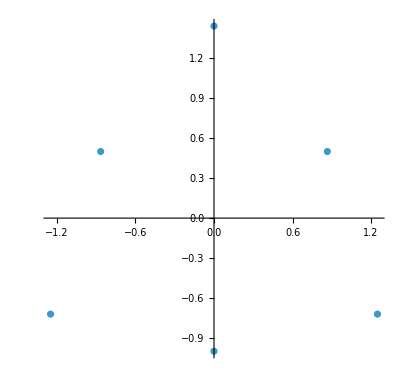

```mathematica
ComplexListPlot[SolveValues[z^6+2I z^3+3==0, z]]
```

4. Dana je množica . Ugotovi, katere od količin min A, inf A, max A in sup A obstajajo ter jih določi. Vse odgovore natančno utemelji.

```mathematica
A[n_]:=(8n+2)/(4n-1)
FindMinimum[A[n], n]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{2.,{n→1.45564×10^12}}

## 2. kolokvij iz Matematike 1

1. Funkcija  je podana s predpisom

 
Izračunaj naravno definicijsko območje funkcije  in izračunaj kompozitum , kjer je 

g funkcija, ki je za  enaka , sicer pa je enaka .

2. Izračunaj naslednjo limito

.

3. V odvisnosti od  preuči konvergenco zaporednja , ki je podano rekurzivno: , , kjer je  naravno število. V primerih ko zaporedje konvergira, zapiši še njegovo limito.

4. Poišči vsa realna števila , za katera konvergira vrsta 

.

## 3. kolokvij iz Matematike 1

-Graphics-